Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[325],OddQ]
nFaulhaber[2,5]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{325,61,23,35,53,5,1}

55

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes Apostol MFDSNT

1. Elliptic Functions

## 1.1 Introduction

## 1.2 Doubly periodic functions

## 1.3 Fundamental pairs of periods

## 1.4 Elliptic functions

### Definition

A function f is called elliptic if it has the following two properties :
- f is doubly periodic;
- f is meromorphic (its only singularities in the finite plane are poles).

### Theorem 1.3

A non-constant elliptic function has a fundamental pair of periods.

#### Proof

=TBD=

### Theorem 1.4

If an elliptic function f has no poles in some period parallelogram, then f is constant.

#### Proof

=TBD=

### Theorem 1.5

If an elliptic function f has no zeros in some period parallelogram, then f is constant.

#### Proof

=TBD=

### Theorem 1.6

The contour integral of an elliptic function taken along the boundary of any cell is zero.

#### Proof

=TBD=

### Theorem 1.7

The sum of the residues of an elliptic function at its poles in any period parallelogram is zero.

#### Proof

=TBD=

### Theorem 1.8

The number of zeros of an elliptic function in any period parallelogram is equal to the number of poles, each counted with multiplicity.

#### Proof

=TBD=

## 1.5 Construction of elliptic functions

## 1.6 The Weierstrass P Function

### Weierstrass Function

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
{p[1+I],p[3+I],p[5-I],p[7+3I]}//N//Chop
{p[-2I],p[2I],p[4I],p[8I]}//N//Chop
```

{0,0,0,0}

{-5.0706×10^30,-5.0706×10^30,-1.26765×10^30,-3.16913×10^29}

```mathematica
ComplexPlot3D[p[z],{z,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot[p[z],{z,0,2+2I},Frame->False]
```

-Graphics-

```mathematica
ComplexPlot[p[z],{z,-2-2I,2+2I}]
```

-Graphics-

#### Some other graphs

### Derivative of Weierstrass Function

```mathematica
p1[z_]:=WeierstrassPPrime[z,WeierstrassInvariants[{1,I}]]
```

```mathematica
p1[1+I]//N//Chop
p1[2+2I]//N//Chop
```

0

-5.70899×10^45-5.70899×10^45 ⅈ

```mathematica
ComplexPlot3D[p1[z],{z,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot[p1[z],{z,-2-2I,2+2I},Frame->False]
```

-Graphics-

#### Zeros of the derivative of the Weierstrass Function

```mathematica
WeierstrassPPrime[2,WeierstrassInvariants[{2,3I}]]//N//Chop
WeierstrassPPrime[3I,WeierstrassInvariants[{2,3I}]]//N//Chop
WeierstrassPPrime[2+3I,WeierstrassInvariants[{2,3I}]]//N//Chop
```

0

0

0

### Identities

```mathematica
tmp=WeierstrassInvariants[{1/2,1/2 I}];
```

```mathematica
WeierstrassP[1/2,tmp]+WeierstrassP[1/2 I,tmp]+WeierstrassP[1/2+1/2 I,tmp]//N//Chop
```

0

```mathematica
WeierstrassPPrime[.2+.1I,WeierstrassInvariants[{1/2,1/2 I}]]^2//N
4(WeierstrassP[.2+.1I,tmp]-WeierstrassP[1/2,tmp])(WeierstrassP[.2+.1I,tmp]-WeierstrassP[1/2 I,tmp])(WeierstrassP[.2+.1I,tmp]-WeierstrassP[1/2+1/2 I,tmp])
```

-30870.9-10068. ⅈ

-30870.9-10068. ⅈ

## 1.7 The Laurent expansion of the Weierstrass function

## 1.8 Differential equation satisfied by the Weierstrass function

### DE-1

```mathematica
DSolve[{y'[x]^2==4 y[x]^3-a y[x]-b}, y[x], x]
```

{{y[x]→WeierstrassP[x-C[1],{a,b}]},{y[x]→WeierstrassP[x+C[1],{a,b}]}}

### DE-2

```mathematica
DSolve[{y''[x]==6 y[x]^2-1/2 b}, y[x], x]
```

{{y[x]→WeierstrassP[x+C[1],{b,C[2]}]}}

## 1.9 The Eisenstein series and the invariants g2 and g3

## 1.10 The numbers e1, e2 and e3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,1I}]]
p[1]//N
p[I]//N
p[1+I]//N
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{4,2I}]]
p[4]//N
p[2I]//N
p[4+2I]//N
```

1.7188

-1.7188

-6.66134×10^-16+3.69779×10^-32 ⅈ

0.21485+0. ⅈ

-0.411268+0. ⅈ

0.196418+2.46519×10^-31 ⅈ

## 1.11 The discrimant

## 1.12 Klein’s modular function J

## 1.13 Invariance of J under unimodular transformations

## 1.14 The Fourier expansions of g2 and g3

## 1.15 The Fourier expansions of D and J

## Exercises

### MFDS 1.1

#### Try-out’s

```mathematica
Table[circle[0,a]//Chop,{a,0,1,0.1}]//tf
```

1.5 | 0 | 0
1.40451 | 0 | 0.293893
1.15451 | 0 | 0.475528
0.845492 | 0 | 0.475528
0.595492 | 0 | 0.293893
0.5 | 0 | 0
0.595492 | 0 | -0.293893
0.845492 | 0 | -0.475528
1.15451 | 0 | -0.475528
1.40451 | 0 | -0.293893
1.5 | 0 | 0

```mathematica
circle1[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}
circle2[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}

circlePlot1=ParametricPlot3D[circle1[u,0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
circlePlot2=ParametricPlot3D[circle2[u,1.0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];

pointPlot=Graphics3D[{Red,PointSize[0.025],Point[{4,0,0}]}];

Show[circlePlot1,circlePlot2,pointPlot,PlotRange->{{-5,8},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
ClearAll[x,y,z,r,θ]
data=CoordinateTransformData[];
```

```mathematica
CoordinateTransformData["Cylindrical" -> "Cartesian","Mapping", {r,θ,z}]
CoordinateTransformData["Cartesian" -> "Cylindrical","Mapping", {x,y,z}]
```

{r Cos[θ],r Sin[θ],z}

{√(x^2+y^2),ArcTan[x,y],z}

```mathematica
Det[{{1,3},{4,5}}]
Det[Transpose[{{1,3},{4,5}}]]
Det[Transpose[{{1,4},{3,5}}]]
```

-7

-7

-7

#### Answer

```mathematica
ClearAll[torus]
torus[u_,v_]:={(1+1/2 Cos[2 Pi v])Cos[2 Pi u],(1+1/2 Cos[2 Pi v])Sin[2 Pi u],1/2 Sin[2 Pi v]}
torus[u_,v_]:={(2+Cos[2 Pi v])Cos[2 Pi u],(2+Cos[2 Pi v])Sin[2 Pi u],Sin[2 Pi v]}

torusPLot=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot1=ParametricPlot3D[torus[u,0],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot2=ParametricPlot3D[torus[0,u],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];

Show[torusPLot]
Show[knotPlot1]
Show[knotPlot2]
Show[torusPLot,knotPlot1,knotPlot2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### MFDS 1.2

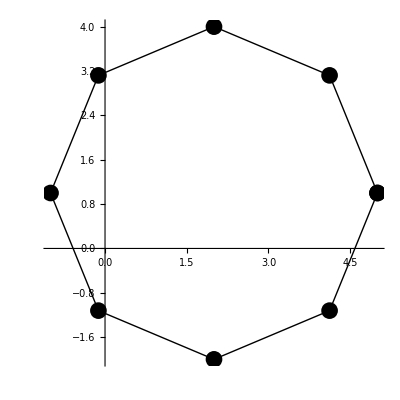

```mathematica
pad=2+I+3cPath[8];
cPlotPath[pad,AxesOrigin->{0,0}]
```

```mathematica
f[z_]:=(z-2-2I)/((z-1)(z-2)(z-3))
g[z_]:=1/f[z]
1/(2π I)cContourIntegral[f'[z]/f[z],z,pad]
1/(2π I)cContourIntegral[g'[z]/g[z],z,pad]
Residue[f[z],{z,1}]
Residue[f[z],{z,2}]
Residue[f[z],{z,3}]
```

-2

2

-1/2-ⅈ

2 ⅈ

1/2-ⅈ

```mathematica
ClearAll[f]
f[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
Integrate[z f'[z]/f[z],{z,2,2+I}]-Integrate[z f'[z]/f[z],{z,0,2+I}]//N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.+1.6307264337491272247061977852624818327001639744350376180560574377×10^-29 ⅈ}. NIntegrate obtained -597.21-1.5708 ⅈ and 92.9891 for the integral and error estimates.

-594.069-6.28319 ⅈ

```mathematica
ClearAll[f]
Integrate[f'[z]/f[z],z]
D[Log[f[z]],{z,1}]
```

Log[f[z]]

f'[z]/f[z]

### MFDS 1.3

### MFDS 1.4

### MFDS 1.5

### MFDS 1.6

### MFDS 1.7

### MFDS 1.8

### MFDS 1.9

### MFDS 1.10

### MFDS 1.11

### MFDS 1.12

### MFDS 1.13

### MFDS 1.14

### MFDS 1.15

## tmp

### tmp-1

```mathematica
g[fun_]:={FunctionInjective[fun[x],x],FunctionSurjective[fun[x],x],FunctionBijective[fun[x],x]}
```

```mathematica
g[Sin]
g[Tan]
g[Exp]
g[#^3&]
```

{False,False,False}

{False,True,False}

{True,False,False}

{True,True,True}

```mathematica
f[x_,y_]:=x^2+y/;{x,y}≠{2,2}
Sum[f[j,k],{j,1,3},{k,1,3}]-f[2,2]
```

54

```mathematica
WeierstrassP[.2+.3I,{1,I}]
```

-2.96065-7.09502 ⅈ

```mathematica
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,0,0},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,0,0}
]/;{w1,w2}≠{0,0}
```

```mathematica
k=10;
f[.2+.3I,2,2I]
k=1000;
f[.2+.3I,2,2I]
```

-3.16452-5.99215 ⅈ

-3.16886-3.71288 ⅈ

```mathematica
WeierstrassP[.2+.3I,{1,I}]
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,100},{j,1,100}
]/;{w1,w2}≠{0,0}
```

-2.96065-7.09502 ⅈ

```mathematica
f[.2+.3I,1,I]
```

-3.36632+2.11861 ⅈ

```mathematica
1/(2.2+2.3I)^2
```

-0.00438524-0.0986192 ⅈ

```mathematica
WeierstrassP[2.2+2.3I,{2,2I}]
f[z_,w1_,w2_]:=1/z^2+Sum[
Piecewise[{{1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2,{i,j}≠{0,0}},{0,True}}],
{i,-k,k},{j,-k,k}]/;{w1,w2}≠{0,0}
k=0;
f[2.2+2.3I,2,2I]
k=15;
f[2.2+2.3I,2,2I]
```

-7.53012-12.3981 ⅈ

-0.00438524-0.0986192 ⅈ

-2.98777-7.03242 ⅈ

```mathematica
g[z_,w1_,w2_,i_,j_]:=1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2
g[.2+.3I,1,I,110050,175]
```

-3.02261×10^-16-4.48734×10^-16 ⅈ

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,20}]//Normal
```

1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)

```mathematica
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)
```

```mathematica
WeierstrassP[0.05+0.05I,{6,111I}]
WeierstrassP[0.05+0.05I,{6,101I}]
WeierstrassP[0.05+0.05I,{2,2I}]
g[0.05+0.05I]
```

2.44249×10^-14-199.999 ⅈ

-2.44249×10^-14-199.999 ⅈ

6.43929×10^-15-200. ⅈ

8.3268×10^-15-199.997 ⅈ

```mathematica
WeierstrassP[1+I, WeierstrassInvariants[{1, I}]]//N//Chop
```

0

```mathematica
DSolve[{y''[x]==x  y[x]}, y[x], x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
f[z_]:=Sin[z]/z
g[w_]:=(Series[f[z],{z,0,18}]//Normal)/.z:> w
h[w_]:=Sinc[w]
```

```mathematica
f[0.1]//N
g[0.1]//N
h[0.1]//N
Limit[f[z],z->0]
```

0.998334

0.998334

0.998334

1

```mathematica
Series[Sin[z]/z,{z,0,6}]
Series[Sinc[z],{z,0,6}]
```

1-z^2/6+z^4/120-z^6/5040+O[z]^7

1-z^2/6+z^4/120-z^6/5040+O[z]^7

```mathematica
(Series[ⅇ^(1/z),{z,Infinity,12}]//Normal)
```

1+1/(479001600 z^12)+1/(39916800 z^11)+1/(3628800 z^10)+1/(362880 z^9)+1/(40320 z^8)+1/(5040 z^7)+1/(720 z^6)+1/(120 z^5)+1/(24 z^4)+1/(6 z^3)+1/(2 z^2)+1/z

```mathematica
Residue[1/(z-1),{z,1}]
```

1

```mathematica
f[z_]:=ⅇ^(1/z)
f[.1+.1I]
f[.01+.1I]
f[.001+.1I]
f[.0001+.0001I]
f[.0001+.001I]
```

42.0992+142.317 ⅈ

-2.39204+1.23383 ⅈ

-0.927909+0.600303 ⅈ

4.58998352293687×10^2170+2.93191724614707×10^2171 ⅈ

-8.77757×10^42+4.76476×10^42 ⅈ

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x,{x,-Infinity,Infinity}]
```

π/2

π

```mathematica
Log[1]
```

0

```mathematica
ⅇ^(1+(1+2π )I)//N
ⅇ^(1+(1+12π )I)//N
ⅇ^(1+(1+26π )I)//N
```

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

```mathematica
Log[1.4686939399158856+1+(1+26π )I]//N
```

4.41544+1.54095 ⅈ

```mathematica
Exp[Log[1/2+3I]-80 π I]//FullSimplify
```

1/2+3 ⅈ

```mathematica
FunctionAnalytic[Log[z],z,Complexes]
```

False

```mathematica
11.07/π
```

3.52369

```mathematica
Log[1]
```

0

```mathematica
f[t_]:=Log[4+ⅇ^(I t)]
f[0.]
f[6 π]//N
f[16 π]//N
```

1.60944+0. ⅈ

1.60944

1.60944

```mathematica
Series[1/(z-1),{z,Infinity,6}]
Series[1/(1-1/2 z),{z,0,6}]
```

1/z+(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

1+z/2+z^2/4+z^3/8+z^4/16+z^5/32+z^6/64+O[z]^7

```mathematica
1/(z-1)+1/(1-1/2 z)//Factor
```

-z/((-2+z) (-1+z))

```mathematica
Series[z ⅇ^(1/z),{z,Infinity,12}]
```

z+1+1/(2 z)+1/(6 z^2)+1/(24 z^3)+1/(120 z^4)+1/(720 z^5)+1/(5040 z^6)+1/(40320 z^7)+1/(362880 z^8)+1/(3628800 z^9)+1/(39916800 z^10)+1/(479001600 z^11)+1/(6227020800 z^12)+O[1/z]^13

```mathematica
Apart[1/((z-1)(z-2)),z]
```

1/(-2+z)-1/(-1+z)

```mathematica
Series[ⅇ^(1/z),{z,Infinity,12}]
```

1+1/z+1/(2 z^2)+1/(6 z^3)+1/(24 z^4)+1/(120 z^5)+1/(720 z^6)+1/(5040 z^7)+1/(40320 z^8)+1/(362880 z^9)+1/(3628800 z^10)+1/(39916800 z^11)+1/(479001600 z^12)+O[1/z]^13

```mathematica
Series[1/((z-1)(z-2)),{z,0,4}]
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+O[z]^5

```mathematica
(Series[1/(z-2),{z,0,4}]//Normal)-(Series[1/(z-1),{z,0,4}]//Normal)
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32

```mathematica
Series[1/(z-2),{z,0,4}]//Normal
```

-1/2-z/4-z^2/8-z^3/16-z^4/32

```mathematica
Series[1/(z-1),{z,Infinity,12}]//Normal
```

1/z^12+1/z^11+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z

```mathematica
Apart[1/(z(z-1)),z]
```

1/(-1+z)-1/z

```mathematica
Series[1/(z(z-1)),{z,0,6}]
```

-1/z-1-z-z^2-z^3-z^4-z^5-z^6+O[z]^7

```mathematica
Series[1/(z(z-1)),{z,Infinity,6}]
```

(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

```mathematica
DSolve[{-y[t]==x'[t],x[t]==y'[t]},{y[t],x[t]},t]
```

{{x[t]→C[1] Cos[t]-C[2] Sin[t],y[t]→C[2] Cos[t]+C[1] Sin[t]}}

```mathematica
m:={{4,-1},{0,0.25}}
m.{{1+0.5I},{0.5-2I}}//mf
```

(3.5+4. ⅈ
0.125-0.5 ⅈ)

```mathematica
Orthogonalize[{{3/2,1},{-2,-1/2}}]
```

{{3/(√13),2/(√13)},{-2/(√13),3/(√13)}}

```mathematica
{3/2,1}.{-2,-1/2}
```

-7/2

```mathematica
{3/(√13),2/(√13)}.{-2/(√13),3/(√13)}
```

0

```mathematica
(3/(√13))^2+(2/(√13))^2
```

1

### tmp-2

```mathematica
rr=3;
torus[u_,v_]:={(rr+Cos[2 Pi u]) Cos[2 Pi v],(rr+Cos[2 Pi u]) Sin[2 Pi v],Sin[2 Pi u]}
tor=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},Boxed->False,MeshStyle->None];
knt=ParametricPlot3D[torus[1,u],{u,0,1},Boxed->False,Axes->False];
grp0=Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}];
grp1=Graphics3D[{PointSize[0.02],Point[{0,4,0.5}]}];
Show[tor,knt,grp1]
```

-Graphics3D-

```mathematica
Show[knt,grp1]
```

-Graphics3D-

### tmp-3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
p[5.35]//N//Chop
p[5.35+17(2+2I)]//N//Chop
```

2.62542

2.62542

```mathematica
123
```

123

```mathematica
Solve[WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]==WeierstrassP[x,WeierstrassInvariants[{1,I}]],x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→ConditionalExpression[(0.6+1.4 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]},{x→ConditionalExpression[(1.4+0.6 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]}}

```mathematica
WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[0.6+1.4I+3000(2+2I),WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[2.6+3.4I+111(2+2I),WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[3.2+4.8I+101(2+2I),WeierstrassInvariants[{1,I}]]//Chop
```

0.+1.00495 ⅈ

0.+1.00495 ⅈ

0.+1.00495 ⅈ

0.+0.237237 ⅈ

```mathematica
((1.5+1.4I+3000(2+2I))+(0.5+0.6I+111(2+2I)))/(2+2I)
```

3112.+0. ⅈ

```mathematica
WeierstrassP[7.25+10.5I,WeierstrassInvariants[{1,I}]]//N
WeierstrassP[1.25+4.5I,WeierstrassInvariants[{1,I}]]//N
```

0.603561+0.717759 ⅈ

0.603561+0.717759 ⅈ

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{1,I}]]
u=1.2+1.2I
v=0.3+0.7I
f[u+v]-f[u-v]//N
-(f'[u]f'[v])/(f[u]-f[v])^2//N
f[.75+.85I]//N
f[1.25+1.15I]//N
```

1.2+1.2 ⅈ

0.3+0.7 ⅈ

2.99571-1.15055 ⅈ

2.99571-1.15055 ⅈ

-0.119239-0.221675 ⅈ

-0.119239-0.221675 ⅈ

```mathematica
ClearAll[f]
DSolve[f'[x]==√q[f[x]],f[x],x]
```

{{f[x]→InverseFunction[1/(√q[K[1]])K[1]1#1&][x+C[1]]}}

### tmp-4

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{2,2I}]]
g[x_]:=((f[x]-f[0.25+2.0I])(f[x]-f[1.25+1.5I]))/((f[x]-f[0.5+I])(f[x]-f[2.0+I])(f[x]-f[3.5+I]))
```

```mathematica
ComplexPlot3D[g[z],{z,0,4+4I}]
```

-Graphics3D-

```mathematica
ComplexPlot[g[z],{z,-4-4I,4+4I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ColorData["Gradients"]//tf;
```